```mathematica
eq1= x+y+z;
eq2=x^2-y^2 -z;
eq3=-x +6 y -z;
Meq={eq1==4,eq2==2,eq3==-2};
sol = Solve[Meq,{x,y,z}]
```

{{x→1/14 (-7-√1185),y→2/7,z→1/14 (59+√1185)},{x→1/14 (-7+√1185),y→2/7,z→1/14 (59-√1185)}}

```mathematica
(*------------------------------------------*)
```

```mathematica
sup1= 4-x-y;
sup2=x^2-y^2-2;
sup3=-x + 6 y +2;
Plot3D[{sup1,sup2,sup3},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
sup[1]= 4-x-y;
sup[2]=x^2-y^2-2;
sup[3]=-x + 6 y +2;
Plot3D[Table[sup[i],{i,1,3}] , {x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
(*------------------------------------------*)
```

```mathematica
lz=MatrixForm[{{1,0,0},{0,0,0},{0,0,-1}}];
lp[i_,j_]:=Sqrt[2] Delta[i, j+1];
lm[i_,j_]:=Sqrt[2] Delta[i, j-1];
```

```mathematica
(*------------------------------------------*)
```

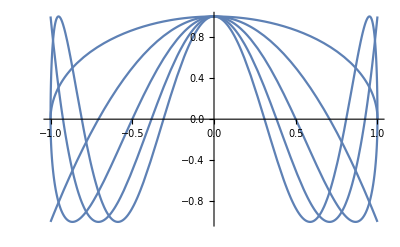

```mathematica
soluz[n_]= y[x] /.DSolve[ (1-x^2) y''[x] -x y'[x] + n^2 y[x] ==0, y[x] , x];
soluz[n_]=soluz[n]/.{C[1]->1 , C[2]->0};
Plot[Table[soluz[n],{n,1,5}],{x,-1,1}]
```

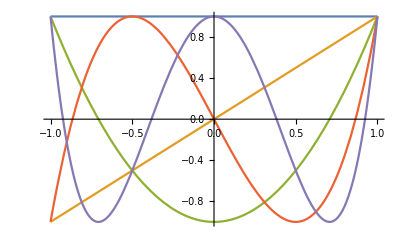

```mathematica
T[0,x_]=1;
T[1,x_]:=x;
T[n_,x]:= 2 x T[n-1,x] - T[n-2,x];
primi5=Table[ T[i,x],{i,0,4}];
Plot[primi5 , {x,-1,1}]
```